# Circuit Implementation of Phase Estimation, Order Finding and Shor's Factoring Algorithm

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to simulate the quantum circuit implementations of Phase Estimation, Order Finding, and Shor's Factoring Algorithms.
Provided that we have a quantum gate u and its powers, and an eigenstate of u, the Phase Estimation Algorithm (PEA) gives (an approximation to) the phase ϕ of the corresponding eigenvalue ⅇ^(2π ⅈ ϕ) in a binary representation. An important application of PEA is the Quantum Order Finding. Let us assume two positive integers x and n, with x<n, that are co-primes (their greatest common divisor is one, gcd(x,n)=1). The order of x in modulo n is defined as the least natural number r such that x^r mod n=1. Quantum Order Finding is a procedure for obtaining the order r of x in modulo n. It is just the PEA applied to a special kind of quantum gate. Shor's Factoring Algorithm uses Quantum Order Finding to return nontrivial factors of an integer. On a quantum computer, to factor an integer N, Shor's algorithm runs in polynomial time (the time taken is polynomial in log N, which is the size of the input). Specifically it takes time O((log (N))^3), demonstrating that the integer factorization problem can be efficiently solved on a quantum computer.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package.

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## Three-Bits Exact Calculation of the Phase of an Eigenvalue

Provided that we have a quantum gate u and its powers, and an eigenstate of u, the Phase Estimation Algorithm (PEA) gives (an approximation to) the phase ϕ of the corresponding eigenvalue ⅇ^(2π ⅈ ϕ) in a binary representation. Below we create a new quantum gate, u. In this first example, the gate u is identical to the standard quantum gate 𝒯_(q̂)

```mathematica
SetQuantumGate[u,1,Function[{q},Subscript[𝒯, q̂]]]
```

The expression u is a quantum gate of 1 arguments (qubits)

These are the eigenvalues and eigenstates of our new gate:

```mathematica
QuantumEigensystemForm[Subscript[u, OverHat[u1]]]
```

Eigenvalue | Eigenvector
1 | |0_OverHat[u1]⟩
(1+ⅈ)/(√2) | |1_OverHat[u1]⟩

We will work with the second eigenvalue in the table. We store it with its eigenstate in the variable mypairu:

```mathematica
mypairu=QuantumEigensystem[Subscript[u, OverHat[u1]]][[All,2]]
```

{(1+ⅈ)/(√2),|1_OverHat[u1]⟩}

We store the eigenstate in |eu⟩:

```mathematica
|eu⟩=mypairu[[2]]
```

|1_OverHat[u1]⟩

We store the eigenvalue in the variable myeigenvalueu:

```mathematica
myeigenvalueu=mypairu[[1]]
```

(1+ⅈ)/(√2)

The gate is unitary, therefore each of its eigenvalues can be written in the form ⅇ^(2 π ⅈ ϕ). Below we use the command NSolve in order to find the value of ϕ for our eigenvalue. We can ignore the warning message, because we are interested only in the value of ϕ such that  0≤ϕ≤1. The solution, which includes the desired value of ϕ, is stored in the variable mysolu:

```mathematica
mysolu=Chop[NSolve[ⅇ^(2π  ⅈ  ϕ)==myeigenvalueu,ϕ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-0.875},{ϕ→0.125}}

Below we extract the positive value of ϕ from the variable mysolu and write it as a base-2 fraction. These base-2 fraction is the expected answer from the Phase Estimation Algorithm (PEA) and it is stored in the variable myexpectedansweru:

```mathematica
myexpectedansweru=BaseForm[Select[ϕ/.mysolu,Positive],2]
```

{0.001_2}

Below we have the Quantum Computing Circuit implementation of the PEA for obtaining an estimation of three bits (qubits) to the phase for a gate u. Notice that the gates u and its powers work on the eigenstate|eu⟩, which in this first example needs only one qubit (u1). On the other hand, the estimated phase will be represented as a three-bits (1,2,3) binary fraction.

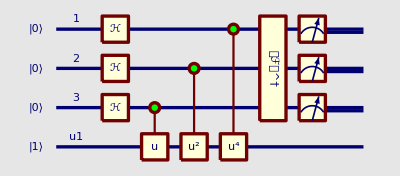

```mathematica
na=3;
nb=1;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"u"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[u, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|eu⟩,ra]]
```

Writting QuantumEvaluate instead of QuantumPlot performs the simulation of the circuit, as shown below. In this example, we obtained the exact representation binary fraction representing the fase ((.001)_2), because enough bits (three, 1,2,3) were used, and we get this phase with probability one:

```mathematica
na=3;
nb=1;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"u"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[u, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|eu⟩,ra]];
TraditionalForm[qe]
```

Probability | Measurement | State
1. | (0_1 | 0_2 | 1_3) | |0⟩⊗|0⟩⊗|1⟩⊗(1. |1⟩)
Probability | Measurement | State

We can compare the result of the measurement above with the expected answer below. In this first example, they are identical:
(0_1 | 0_2 | 1_3)→(.001)_2

```mathematica
myexpectedansweru
```

{0.001_2}

## Two-Bits Approximation to the Phase of an Eigenvalue

In this example a two-qubit gate, w, will be used. This particular gate is made of the standard quantum gates 𝒮𝒲𝒜𝒫_(OverHat[q1],OverHat[q2])·𝒯_OverHat[q1]·𝒳_OverHat[q2]:

```mathematica
SetQuantumGate[w,2,Function[{q1,q2},Subscript[𝒮𝒲𝒜𝒫, OverHat[q1],OverHat[q2]]·Subscript[𝒯, OverHat[q1]]·Subscript[𝒳, OverHat[q2]]]]
```

The expression w is a quantum gate of 2 arguments (qubits)

Below we have the eigenvalues and eigenstates for our new gate w:

```mathematica
TraditionalForm[QuantumEigensystemForm[Subscript[w, OverHat[w1],OverHat[w2]]]]
```

Eigenvalue | Eigenvector
-cos(π/8)-ⅈ sin(π/8) | 1/2 |00⟩+1/2 |11⟩+(-((1/2-ⅈ/2) sin(π/8))/(√2)-((1/2+ⅈ/2) cos(π/8))/(√2)) |01⟩+(-((1/2+ⅈ/2) sin(π/8))/(√2)-((1/2-ⅈ/2) cos(π/8))/(√2)) |10⟩
cos(π/8)+ⅈ sin(π/8) | 1/2 |00⟩+1/2 |11⟩+(((1/2-ⅈ/2) sin(π/8))/(√2)+((1/2+ⅈ/2) cos(π/8))/(√2)) |01⟩+(((1/2+ⅈ/2) sin(π/8))/(√2)+((1/2-ⅈ/2) cos(π/8))/(√2)) |10⟩
-sin(π/8)+ⅈ cos(π/8) | -1/2 |00⟩+1/2 |11⟩+(((1/2-ⅈ/2) cos(π/8))/(√2)-((1/2+ⅈ/2) sin(π/8))/(√2)) |01⟩+(((1/2+ⅈ/2) cos(π/8))/(√2)-((1/2-ⅈ/2) sin(π/8))/(√2)) |10⟩
sin(π/8)-ⅈ cos(π/8) | -1/2 |00⟩+1/2 |11⟩+(((1/2+ⅈ/2) sin(π/8))/(√2)-((1/2-ⅈ/2) cos(π/8))/(√2)) |01⟩+(((1/2-ⅈ/2) sin(π/8))/(√2)-((1/2+ⅈ/2) cos(π/8))/(√2)) |10⟩

We will use the third eigenvalue in the table. Below it is stored together with the corresponding eigenstate in the variable mypairw:

```mathematica
mypairw=QuantumEigensystem[Subscript[w, OverHat[w1],OverHat[w2]]][[All,3]]
```

{ⅈ Cos[π/8]-Sin[π/8],-1/2 |0_OverHat[w1],0_OverHat[w2]⟩+(((1/2-ⅈ/2) Cos[π/8])/(√2)-((1/2+ⅈ/2) Sin[π/8])/(√2)) |0_OverHat[w1],1_OverHat[w2]⟩+(((1/2+ⅈ/2) Cos[π/8])/(√2)-((1/2-ⅈ/2) Sin[π/8])/(√2)) |1_OverHat[w1],0_OverHat[w2]⟩+1/2 |1_OverHat[w1],1_OverHat[w2]⟩}

Below the eigenstate is stored in |ew⟩:

```mathematica
|ew⟩=mypairw[[2]]
```

-1/2 |0_OverHat[w1],0_OverHat[w2]⟩+(((1/2-ⅈ/2) Cos[π/8])/(√2)-((1/2+ⅈ/2) Sin[π/8])/(√2)) |0_OverHat[w1],1_OverHat[w2]⟩+(((1/2+ⅈ/2) Cos[π/8])/(√2)-((1/2-ⅈ/2) Sin[π/8])/(√2)) |1_OverHat[w1],0_OverHat[w2]⟩+1/2 |1_OverHat[w1],1_OverHat[w2]⟩

Below the eigenvalue is stored in myeigenvaluew:

```mathematica
myeigenvaluew=mypairw[[1]]
```

ⅈ Cos[π/8]-Sin[π/8]

Below we get the phase ϕ of the eigenvalue ⅇ^(2 π ⅈ ϕ). We can ignore the warning about other solutions being lost, because we are interested only in the value of ϕ such that 0≤ϕ≤1:

```mathematica
mysolw=Chop[NSolve[ⅇ^(2π  ⅈ  ϕ)==myeigenvaluew,ϕ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-0.6875},{ϕ→0.3125}}

Below we select the positive value of ϕ, represent it as a binary fraction and store it in myexpectedanswerw. Notice that 4 bits are necesary to write this particular phase:

```mathematica
myexpectedanswerw=BaseForm[Select[ϕ/.mysolw,Positive],2]
```

{0.0101_2}

We will calculate a two-bits aproximation to the four-bits phase. Below is the circuit. The first register (1,2) contains the result of the calculation, and the second register (w1,w2) must be initialized to the eigenstate whose eigenvalue we want to calculate.

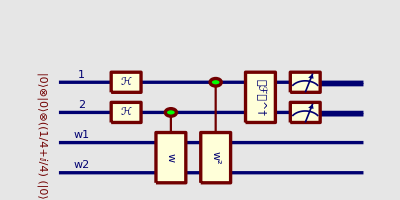

```mathematica
na=2;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|ew⟩,ra]]
```

Replace QuantumPlot with QuantumEvaluate to simulate the circuit operation, as shown below. Notice that the best two-bits aproximation to the real phase ((.0101)_2) is the binary fraction (.01)_2, and that the digits of this approximation are obtained 82% of the measurements of qubits (1,2),as shown below. Notice the use of the command TraditionalForm and the option FactorKet→False in order to have a nicer output:

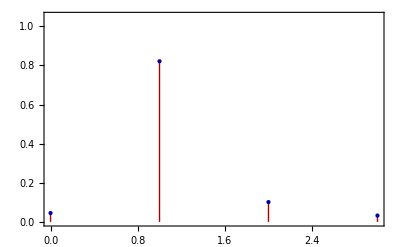
-Graphics-
Probability | Measurement | State
0.045202 | (0_1 | 0_2) | (-0.490393+0.0975452 ⅈ) |0000⟩+(0.0975452-0.490393 ⅈ) |0001⟩+(0.277785+0.415735 ⅈ) |0010⟩+(0.490393-0.0975452 ⅈ) |0011⟩
0.821067 | (0_1 | 1_2) | (-0.415735-0.277785 ⅈ) |0100⟩+(0.415735-0.277785 ⅈ) |0101⟩-(0.0975452-0.490393 ⅈ) |0110⟩+(0.415735+0.277785 ⅈ) |0111⟩
0.101245 | (1_1 | 0_2) | (0.0975452+0.490393 ⅈ) |1000⟩-(0.490393+0.0975452 ⅈ) |1001⟩+(0.415735-0.277785 ⅈ) |1010⟩-(0.0975452+0.490393 ⅈ) |1011⟩
0.0324864 | (1_1 | 1_2) | (-0.277785+0.415735 ⅈ) |1100⟩-(0.277785+0.415735 ⅈ) |1101⟩+(0.490393+0.0975452 ⅈ) |1110⟩+(0.277785-0.415735 ⅈ) |1111⟩
Probability | Measurement | State

```mathematica
na=2;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|ew⟩,
ra,FactorKet->False]];
Column[{
QuantumPlot[qe],
TraditionalForm[qe]
}]
```

82% of the measurements the circuit (above) will give the binary fraction (0_1 | 1_2)→(.01)_2, which corresponds to the decimal fraction ϕ_aprox=0.25 as a two-bit approximation to the real value (.0101)_2=0.3125

```mathematica
myexpectedanswerw
```

{0.0101_2}

## Three-Bits Approximation to the Phase of an Eigenvalue

Below we have the circuit to give a three-bits approximation to same phase as in the previous section:

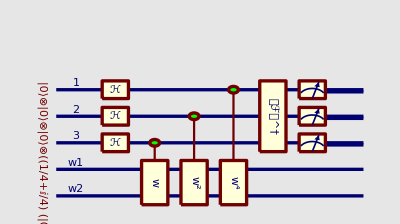

```mathematica
na=3;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|ew⟩,ra]]
```

Below is the simulation of the circuit. Notice that there are two "good" three-bits approximations to the real phase ((.0101)_2): the binary fraction (.010)_2, and the binary fraction (.011)_2, each one of them will be obtained as a result 41% of the measurements, therefore the cicuit will give a good approximation to the phase 82% of the measurements. This simulation can take several minutes in your computer.

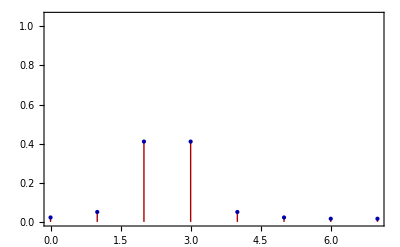
-Graphics-
Probability | Measurement | State
0.022601 | (0_1 | 0_2 | 0_3) | (-0.415735-0.277785 ⅈ) |00000⟩+(0.415735-0.277785 ⅈ) |00001⟩-(0.0975452-0.490393 ⅈ) |00010⟩+(0.415735+0.277785 ⅈ) |00011⟩
0.0506223 | (0_1 | 0_2 | 1_3) | (-0.277785-0.415735 ⅈ) |00100⟩+(0.490393-0.0975452 ⅈ) |00101⟩-(0.277785-0.415735 ⅈ) |00110⟩+(0.277785+0.415735 ⅈ) |00111⟩
0.410533 | (0_1 | 1_2 | 0_3) | (-0.0975452-0.490393 ⅈ) |01000⟩+(0.490393+0.0975452 ⅈ) |01001⟩-(0.415735-0.277785 ⅈ) |01010⟩+(0.0975452+0.490393 ⅈ) |01011⟩
0.410533 | (0_1 | 1_2 | 1_3) | (-0.0975452+0.490393 ⅈ) |01100⟩-(0.415735+0.277785 ⅈ) |01101⟩+(0.490393-0.0975452 ⅈ) |01110⟩+(0.0975452-0.490393 ⅈ) |01111⟩
0.0506223 | (1_1 | 0_2 | 0_3) | (-0.277785+0.415735 ⅈ) |10000⟩-(0.277785+0.415735 ⅈ) |10001⟩+(0.490393+0.0975452 ⅈ) |10010⟩+(0.277785-0.415735 ⅈ) |10011⟩
0.022601 | (1_1 | 0_2 | 1_3) | (-0.415735+0.277785 ⅈ) |10100⟩-(0.0975452+0.490393 ⅈ) |10101⟩+(0.415735+0.277785 ⅈ) |10110⟩+(0.415735-0.277785 ⅈ) |10111⟩
0.0162432 | (1_1 | 1_2 | 0_3) | (-0.490393+0.0975452 ⅈ) |11000⟩+(0.0975452-0.490393 ⅈ) |11001⟩+(0.277785+0.415735 ⅈ) |11010⟩+(0.490393-0.0975452 ⅈ) |11011⟩
0.0162432 | (1_1 | 1_2 | 1_3) | (-0.490393-0.0975452 ⅈ) |11100⟩+(0.277785-0.415735 ⅈ) |11101⟩+(0.0975452+0.490393 ⅈ) |11110⟩+(0.490393+0.0975452 ⅈ) |11111⟩
Probability | Measurement | State

```mathematica
na=3;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|ew⟩,
ra,FactorKet->False]];
Column[{
QuantumPlot[qe],
TraditionalForm[qe]
}]
```

QuantumPlot3D gives a nice 3D graph of the probabilities:

```mathematica
QuantumPlot3D[qe]
```

-Graphics3D--Graphics- | {0_1,0_2,0_3}
-Graphics- | {0_1,0_2,1_3}
-Graphics- | {0_1,1_2,0_3}
-Graphics- | {0_1,1_2,1_3}
-Graphics- | {1_1,0_2,0_3}
-Graphics- | {1_1,0_2,1_3}
-Graphics- | {1_1,1_2,0_3}
-Graphics- | {1_1,1_2,1_3}

82% of the measurements the circuit will give either (0_1 | 1_2 | 0_3)→(.010)_2 or (0_1 | 1_2 | 1_3)→(.011)_2, which correspond to the decimal values ϕ_aprox1=0.25 and ϕ_aprox2=0.375, the three-bit approximations to the real value (.0101)_2=0.3125

```mathematica
myexpectedanswerw
```

{0.0101_2}

## Four-Bits Exact Calculation of the Phase of an Eigenvalue

Below we have the circuit to give a four-bits approximation to same phase as in the previous section. 
Notice that the last controlled gate is w^8:

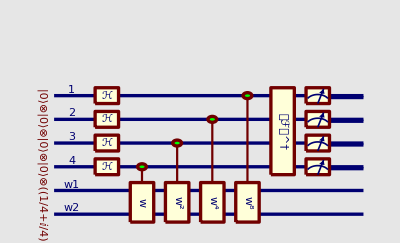

```mathematica
na=4;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|ew⟩,ra]]
```

Four bits are enough for giving the exact answer ((.0101)_2), as can be seen below. 
When the answer is exact, it is obtained with probability one:

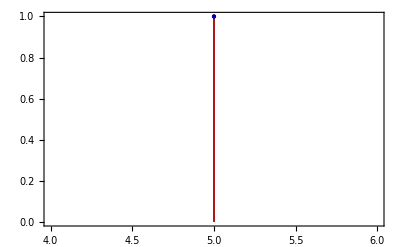
-Graphics-
Probability | Measurement | State
1. | (0_1 | 1_2 | 0_3 | 1_4) | -0.5 |010100⟩+(0.191342-0.46194 ⅈ) |010101⟩+(0.191342+0.46194 ⅈ) |010110⟩+0.5 |010111⟩
Probability | Measurement | State

```mathematica
na=4;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗|ew⟩,
ra,FactorKet->False]];
Column[{
QuantumPlot[qe],
TraditionalForm[qe]
}]
```

We can compare the result of the measurement with the expected answer. In this example, they are identical.
(0_1 | 1_2 | 0_3 | 1_4)→(.0101)_2

```mathematica
myexpectedanswerw
```

{0.0101_2}

## Four-Bits Exact Calculation of the Phase of all the Eigenvalues

We continue working with the same quantum gate w that was defined above. This time we will not use an eigenket of w in the second register of the PEA circuit, therefore we will obtain phases of different eigenvalues with different probabilities. Below are all the eigenvalues of this gate:

```mathematica
alleigenvaluesw=N[QuantumEigensystem[Subscript[w, OverHat[w1],OverHat[w2]]][[1]]]
```

{-0.92388-0.382683 ⅈ,0.92388+0.382683 ⅈ,-0.382683+0.92388 ⅈ,0.382683-0.92388 ⅈ}

Below we calculate the phases for the eigenvalues. The "inverse functions" warning can be ignored, because we are only interested in values such that 0≤ϕ≤1

```mathematica
allsolutionsw=Map[Function[{ei},Chop[NSolve[ⅇ^(2π  ⅈ  ϕ)==ei,ϕ]]],alleigenvaluesw]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve will be suppressed during this calculation.

{{{ϕ→-0.4375},{ϕ→0.5625}},{{ϕ→-0.9375},{ϕ→0.0625}},{{ϕ→-0.6875},{ϕ→0.3125}},{{ϕ→-0.1875},{ϕ→0.8125}}}

Below the positive values of ϕ are selected and transformed to binary fractions. Each phase value ϕ corresponds to an eigenvalue ⅇ^(2π ⅈ ϕ). In this example, each phase can be exactly represented using four bits.

```mathematica
allexpectedanswersw=Map[Function[{sol},BaseForm[Select[ϕ/.sol,Positive],2]],allsolutionsw]
```

{{0.1001_2},{0.0001_2},{0.0101_2},{0.1101_2}}

Below we have the PEA circuit with four qbits in the first register. This time the second register is not initialized to an eigenstate. Instead, it is initialized to the state |00⟩.

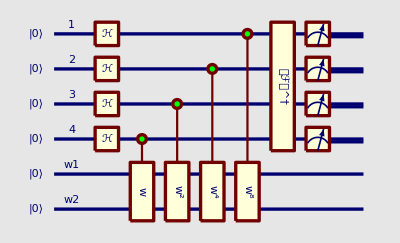

```mathematica
na=4;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗(|0⟩)_rb,ra]]
```

Below we have a simulation of the PEA circuit, with the second register initialized to |00⟩ , which is NOT an eigenstate of w. In this simple example, the four qbits of the first register are enough to represent each one of the eigenvalues, therefore all the measurment results are always phases of eigenvalues of w.

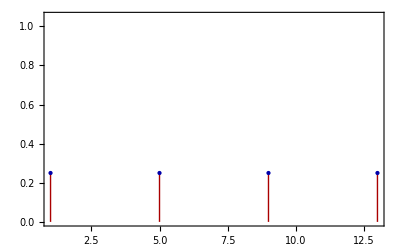
-Graphics-
Probability | Measurement | State
0.25 | (0_1 | 0_2 | 0_3 | 1_4) | 0.5 |000100⟩+(0.46194+0.191342 ⅈ) |000101⟩+(0.46194-0.191342 ⅈ) |000110⟩+0.5 |000111⟩
0.25 | (0_1 | 1_2 | 0_3 | 1_4) | 0.5 |010100⟩-(0.191342-0.46194 ⅈ) |010101⟩-(0.191342+0.46194 ⅈ) |010110⟩-0.5 |010111⟩
0.25 | (1_1 | 0_2 | 0_3 | 1_4) | 0.5 |100100⟩-(0.46194+0.191342 ⅈ) |100101⟩-(0.46194-0.191342 ⅈ) |100110⟩+0.5 |100111⟩
0.25 | (1_1 | 1_2 | 0_3 | 1_4) | 0.5 |110100⟩+(0.191342-0.46194 ⅈ) |110101⟩+(0.191342+0.46194 ⅈ) |110110⟩-0.5 |110111⟩
Probability | Measurement | State

```mathematica
na=4;
nb=2;
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"w"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[w, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗(|0⟩)_rb,
ra,FactorKet->False]];
Column[{
QuantumPlot[qe],
TraditionalForm[qe]
}]
```

Compare the expected answers below, with the possible measurement outcomes above. As each expected answer can be represented with four qbits (for this example), we get only the correct phases as measurment results:
(0_1 | 0_2 | 0_3 | 1_4)→(.0001)_2
(0_1 | 1_2 | 0_3 | 1_4)→(.0101)_2
(1_1 | 0_2 | 0_3 | 1_4)→(.1001)_2
(1_1 | 1_2 | 0_3 | 1_4)→(.1101)_2

```mathematica
allexpectedanswersw
```

{{0.1001_2},{0.0001_2},{0.0101_2},{0.1101_2}}

## Quantum Order Finding

Let us assume two positive integers x and n, with x<n, that are co-primes (their greatest common divisor is one, gcd(x,n)=1). The order of x in modulo n is defined as the least natural number r such that:
x^r mod n=1

Below is the definition of a quantum gate that is used in qauntum order finding.
For two fixed integers x, n, this gate transform state |y⟩ (where y is an integer represented in binary in the qubits) into the state|xy(mod n)⟩ if 0≤y≤n-1 , and leaves|y⟩ unchanged otherwise. 
We will use x=3 and n=11 as an example:

```mathematica
x=3;
n=11;

nqbits=Ceiling[Log[2,n]];
gatename=Symbol["x"<>ToString[x]<>"n"<>ToString[n]];

SetQuantumGate[gatename,nqbits,
Function[
Sum[
If[0≤y≤n-1,
(|Mod[y*x,n]⟩)_{##}·(⟨y|)_{##},
(|y⟩)_{##}·(⟨y|)_{##}  ],
{y,0,2^nqbits-1}
]]]
```

The expression x3n11 is a quantum gate of 4 arguments (qubits)

Below is the truth table for our new gate:

```mathematica
TraditionalForm[QuantumTableForm[Subscript[x3n11, OverHat[1],OverHat[2],OverHat[3],OverHat[4]]]]
```

|   Input |   Output
0 | |0000⟩ | |0000⟩
1 | |0001⟩ | |0011⟩
2 | |0010⟩ | |0110⟩
3 | |0011⟩ | |1001⟩
4 | |0100⟩ | |0001⟩
5 | |0101⟩ | |0100⟩
6 | |0110⟩ | |0111⟩
7 | |0111⟩ | |1010⟩
8 | |1000⟩ | |0010⟩
9 | |1001⟩ | |0101⟩
10 | |1010⟩ | |1000⟩
11 | |1011⟩ | |1011⟩
12 | |1100⟩ | |1100⟩
13 | |1101⟩ | |1101⟩
14 | |1110⟩ | |1110⟩
15 | |1111⟩ | |1111⟩

Below is the matrix representation for our new gate, with nonzero entries shown in color. In this case, all nonzero entries are equal to one:

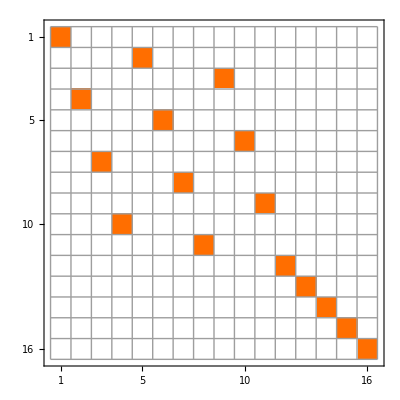

```mathematica
MatrixPlot[QuantumMatrix[Subscript[x3n11, OverHat[1],OverHat[2],OverHat[3],OverHat[4]]],Mesh->All]
```

Below is the circuit for finding the order r of x=3 in modulo n=11. Notice that it is the Phase Estimation Algorithm applied to the gate that transforms  |y⟩→|xy(mod n)⟩, with entry |y⟩=(|1⟩)_Ceiling[log_2(n)] and using Ceiling[log_2(n^2)] qubits for the answer:

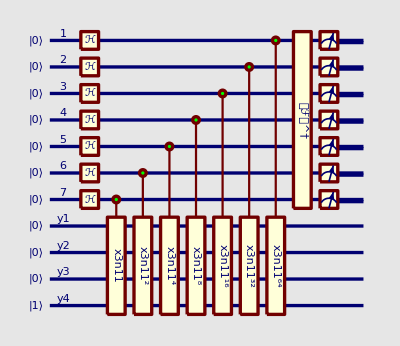

```mathematica
na=Ceiling[Log[2,n^2]];
nb=Ceiling[Log[2,n]];
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"y"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[x3n11, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗(|1⟩)_rb,ra]]
```

Write QuantumEvaluate instead of QuantumPlot, as shown below, in order to run the simulation of the circuit. This simulation takes several hours in a personal computer. As there are many possible measurement outcomes, this time we only show the plot of the probabilities. If you are using Mathematica to read this document, place the cursor on each point of the graph and the corresponding measurement outcome will be displayed. Notice that the complete simulation result is stored in the variable qe:

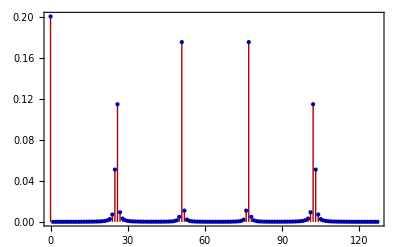

```mathematica
na=Ceiling[Log[2,n^2]];
nb=Ceiling[Log[2,n]];
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"y"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[x3n11, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗(|1⟩)_rb,ra,FactorKet->False]];
QuantumPlot[qe,PlotRange->All]
```

The measurement probability has 5 peaks. If you are using Mathematica to read this document, you can place the cursor on each dot and the measurement (written as a decimal integer) together with the corresponding probability will be displayed. Using this procedure we can verify that the five peaks are the binary digits corresponding to the integers 0, 26, 51, 77 and 102:

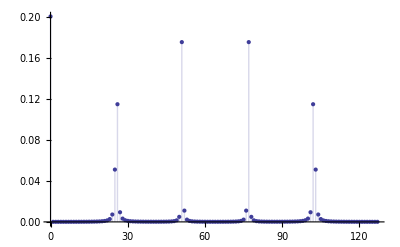

Assume that 51 was obtained in as a measurement result. This means that the binary digits are actually: 
51→110011_2→(0_1 | 1_2 | 1_3 | 0_4 | 0_5 | 1_6 | 1_7).
The complete measurement results were stored in the variable qe, therefore we can see our measurement result using the following standard Mathematica syntax:

```mathematica
TraditionalForm[qe[[1,1+51]]]
```

{0.175086,(0_1 | 1_2 | 1_3 | 0_4 | 0_5 | 1_6 | 1_7),(0.370534+0.260959 ⅈ) |01100110001⟩-(0.142162+0.430331 ⅈ) |01100110011⟩-0.438072 |01100110100⟩+(0.351863-0.260959 ⅈ) |01100110101⟩-(0.142162-0.430331 ⅈ) |01100111001⟩}

The first number in this output is the probability of obtaining this particular outcome. The second element is the actual measurement outcome (the values for each measured qubit). The third element is the state of the system after the measurement:

{0.175086,(0_1 | 1_2 | 1_3 | 0_4 | 0_5 | 1_6 | 1_7),(0.370534+0.260959 ⅈ) |01100110001⟩-(0.142162+0.430331 ⅈ) |01100110011⟩-0.438072 |01100110100⟩+(0.351863-0.260959 ⅈ) |01100110101⟩-(0.142162-0.430331 ⅈ) |01100111001⟩}

This measurement corresponds to the following binary fraction: 
(0_1 | 1_2 | 1_3 | 0_4 | 0_5 | 1_6 | 1_7) → 0.0110011_2 → 51/128 
Now it is necessary to obtain the continued-fraction of the measured fraction:
 b/a=a_0+1/(a_1+1/(a_2+1/(...+1/a_m))) 
The convergents of the fraction are:
a_0, a_0+1/a_1, a_0+1/(a_1+1/a_2), a_0+1/(a_1+1/(a_2+1/a_3)), ...
The (candidate to be the) order r is the denominator of the convergent closest to the fraction with denominator less than n (notice that for our purposes a_0=0 and all the convergents are proper fractions):

```mathematica
Convergents[51/128]
```

{0,1/2,1/3,2/5,51/128}

The denominator of the convergent closest to the fraction with denominator less than n=11  is in this case r=5. We can easily verify that this is the correct answer:

```mathematica
Mod[3^5,11]
```

1

Therefore the order of x=3 in modulo n=11 is r=5 (it is the lowest natural number r such that  x^r mod n=1)

## Shor's Factoring Algorithm:

Shor's Factoring Algorithm (from the book by Nielsen and Chuang)
Inputs: A composite number n.
Outputs: A non-trivial factor of n.
Runtime:  O((log n)^3)  operations. 
Procedure:
1. If n is even, return the factor 2, otherwise continue to the next step.
2. Determine whether n=a^b for integers a≥1 and b≥2, and if so, return the factor a, otherwise continue to the next step.
3. Randomly choose x in the range 1 to n-1. If the greater common divisor of x and n is greater than 1 (gcd(x,n)>1) the return the factor gcd(x,n), otherwise continue to the next step.
4. Use the Quantum Order-Finding algorithm to find the order r of x in modulo n.
5. If r is even and x^(r/2)≠ -1(mod n) then compute gcd(x^(r/2)-1,n) and gcd(x^(r/2)+1,n), and test to see if one of these is a non-trivial factor, returning the factor if so. Otherwise randomly choose another value for x and go back to step 3.

## Quantum Factoring n=15

1. n=15 is not even, therefore we must continue to the next step.
2. 15≠a^b for integers a≥1 and b≥2, therefore we must continue to the next step.
3. Randomly choose x in the range 1 to 15-1. Assume that x=7 was choosen.
The greater common divisor of x=7 and n=15 is exactly 1, therefore we must continue to the next step.

```mathematica
GCD[7,15]
```

1

4. Use the Quantum Order-Finding algorithm for x=7 and n=15.

Below is the definition of a quantum gate that is used in qauntum order finding for x=7 and n=15.

```mathematica
x=7;
n=15;

nqbits=Ceiling[Log[2,n]];
gatename=Symbol["x"<>ToString[x]<>"n"<>ToString[n]];

SetQuantumGate[gatename,nqbits,
Function[
Sum[
If[0≤y≤n-1,
(|Mod[y*x,n]⟩)_{##}·(⟨y|)_{##},
(|y⟩)_{##}·(⟨y|)_{##}  ],
{y,0,2^nqbits-1}
]]]
```

The expression x7n15 is a quantum gate of 4 arguments (qubits)

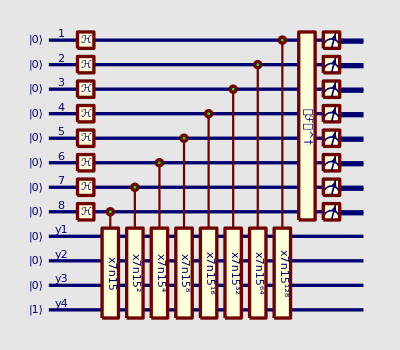

```mathematica
na=Ceiling[Log[2,n^2]];
nb=Ceiling[Log[2,n]];
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"y"];
QuantumPlot[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[x7n15, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗(|1⟩)_rb,ra]]
```

Below is the simulation of the circuit. The output from this circuit has to be further processed to give the order of x=7 in modulo n=15:

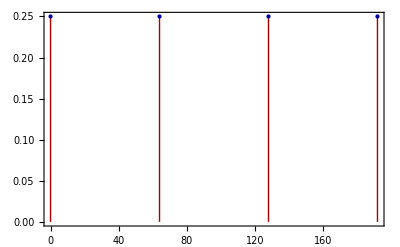

```mathematica
na=Ceiling[Log[2,n^2]];
nb=Ceiling[Log[2,n]];
ra=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[na];
rb=ℛℯℊ𝒾𝓈𝓉ℯ𝓇[nb,"y"];
qe=QuantumEvaluate[
QubitMeasurement[SuperDagger[Subscript[𝒬ℱ𝒯, ra]]·⊗_(k=1)^na(𝒞^{k̂})[(Subscript[x7n15, rb])^(2^(na-k))]·Subscript[ℋ, ra]·(|0⟩)_ra⊗(|1⟩)_rb,ra,FactorKet->False]];
QuantumPlot[qe,PlotRange->All]
```

```mathematica
TraditionalForm[qe]
```

Probability | Measurement | State
0.25 | (0_1 | 0_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8) | 0.5 |000000000001⟩+0.5 |000000000100⟩+0.5 |000000000111⟩+0.5 |000000001101⟩
0.25 | (0_1 | 1_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8) | 0.5 |010000000001⟩-0.5 |010000000100⟩-0.5 ⅈ |010000000111⟩+0.5 ⅈ |010000001101⟩
0.25 | (1_1 | 0_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8) | 0.5 |100000000001⟩+0.5 |100000000100⟩-0.5 |100000000111⟩-0.5 |100000001101⟩
0.25 | (1_1 | 1_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8) | 0.5 |110000000001⟩-0.5 |110000000100⟩+0.5 ⅈ |110000000111⟩-0.5 ⅈ |110000001101⟩
Probability | Measurement | State

We see the possible measurement outputs as binary representations of fractions:
(0_1 | 0_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8)→  0.00000000_2 → 0
(0_1 | 1_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8)→  0.01000000_2 → 1/4
(1_1 | 0_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8)→  0.10000000_2 → 1/2
(1_1 | 1_2 | 0_3 | 0_4 | 0_5 | 0_6 | 0_7 | 0_8)→  0.11000000_2 → 3/4

Notice that two of the fractions have 4 as a denominator. Below we verify that this is the answer: the order of x=7 in modulo n=15 is r=4:

```mathematica
Mod[7^4,15]
```

1

5. We obtained r=4 which is even and x^(r/2)≠ -1(mod n)  (in this example -1(mod n) is equal to 14)

```mathematica
Mod[7^(4/2),15]
```

4

The result above is not equal to -1(mod n), as can be seen below:

```mathematica
Mod[-1,15]
```

14

Then compute gcd(x^(r/2)-1,n) and gcd(x^(r/2)+1,n), and test to see if one of these is a non-trivial factor, returning the factor if so:

```mathematica
{GCD[7^(4/2)-1,15],GCD[7^(4/2)+1,15]}
```

{3,5}

We obtained the factors of 15=3×5

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx